```mathematica
V3[r,Fe,Fh]
```

-1/r-(1.0340694151301588199487468955339863896369934082031 ⅇ^(-1.251248254822574068612084374763071537017822265625 r^2))/r

## Definition

```mathematica
δ50V
```

{-0.0010267187881719285547184166190185026275973868077613,-0.0032467554478780697897824927631444886122078594651864,-0.010266685621300441929106827122409018756250247822583,-0.032451674518663234896694776555766344085923696062639,-0.10216562504626378407153741674126786570525103680313,-0.30901756386521594034884868237194699812922339086679,-0.74203191294269209185057964849708285899059425206038,1.5673736833351293986135293227984249228501266218,0.015524934374466823551254487744579493371028290188832,-0.88744319464309064157171705866912675367338695397641,-0.20224163362987639270492010964404402576249399096653,0.6863486273724055358025889869808937842566683549727,-0.13883946810241228030600565658635463959949715367861,0.57926998587076593877244067927595422948096119912436,-1.0080199840419547770630802398475412680442145787965,1.5500530247663345275431602679138176684043950876,0.058176998706029258758321521062552040519299630855512,-0.80667831867594189884072450511736090869543138572508,-1.1038609333377020361547079986125189179900030533149}

```mathematica
δa[r_]=(E^(-r^2/(2 a^2)))/((2π)^(3/2)a^3);α=1;u0=10^-20;δstart=10^-10;m=1;αSch=2m;
a=1;ee={10^-10,10^-9,10^-8,10^-7,10^-6,10^-5,10^-4,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1,3,7,10};
Vs1[r_,a_,c1_]=- α/r Erf[r/(√2 a)]+c1 a^2 δa[r];
Vs2[r_,a_,{c2_,d1_}]=- 1/# Erf[#/(√2 a)]+c2 a^2 δa[#]+d1 a^4 Laplacian[δa[#],{#,θ,ϕ},"Spherical"]&[r];V1[r_,Fa_]=-α/r+If[0≤r<a,Fa,0];
V2[r_,Fc_,Fd_]=-α/r+Fc E^(-Fd r)/r;
V3[r_,Fe_,Fh_]=-α/r+Fe(E^(-Fh r^2))/r;
```

```mathematica
Fe=-1.034069415130158819948746895533986389636993408203125`50.
Fh=1.251248254822574068612084374763071537017822265625`50.
```

-1.0340694151301588199487468955339863896369934082031

1.251248254822574068612084374763071537017822265625

```mathematica
RS[n_,r_]=2/(A^(3/2) n^(3/2)) ⅇ^(-r/(n A)) Hypergeometric1F1[1-n,2,(2 r)/(n A)]/.A->Rationalize@(1/(m α));
```

```mathematica
EigenEnergy[V_,αSch_,{min_,max_},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
Module[{shift=10,d=1000,n=20,ev},{ev,ef}=NDEigensystem[{shift f[r]+V f[r]-1/αSch f''[r](*+NeumannValue[0,r==d]*),DirichletCondition[f[r]==0,True]},f[r],{r,0,d},n,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.05}}},"Eigensystem"->{"Arnoldi",MaxIterations->Infinity}}];
evShifted=ev-shift];
Print[evShifted];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u'[max]==-min,u[max]==min},u,{r,min,max},e,opt1,MaxSteps->Infinity];
evnew=e/.#&/@
Table[
PrintTemporary[n];FindRoot[u[e][min]==0/.sol,{e,0.99 SetPrecision[evShifted[[n]],3],1.01 SetPrecision[evShifted[[n]],3]},opt2(*,StepMonitor:>PrintTemporary[e]*)],{n,20}]
]
δ50e[en_,V_]:=Module[{sol,δs,δr,r1=50,r2=u0,β,jder,nder,k,wpc=50,prc=20,time1,time2},
time1=SessionTime[];
k=√(2en);
β:=r1 u'[r1]/u[r1]-1;
jder[r_]=D[SphericalBesselJ[0,r],r];
nder[r_]=D[SphericalBesselY[0,r],r];sol=Flatten@NDSolve[{u''[r]+αSch(en-V)u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},PrecisionGoal->prc,WorkingPrecision->wpc, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}(*,SolveDelayed->True*)];
δs=FindRoot[(*u'[r1]/u[r1]==k Cot[k r1+δ]*)Tan[δ]==(k r1 jder[k r1]-β SphericalBesselJ[0,k r1])/(k r1 nder[k r1]-β SphericalBesselY[0,k r1])/.sol,{δ,0},WorkingPrecision->wpc,PrecisionGoal->prc];
δr=δ/.δs;
time2=SessionTime[];
Print["End with "<>ToString[time2-time1]<>"s"];
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&]
]
δ50[V_]:=Module[{en,len,δen,timestampa,timestampb},
len=Length@ee;
ParallelTable[
timestampa=SessionTime[];
en=ee[[i]];
δen=δ50e[en,V];
timestampb=SessionTime[];
Print[{en,δen},"    ",timestampb-timestampa];
δen,{i,2,len}]
]
Eigenfun[V_,enelist_]:=Module[{},Flatten[With[{r1=2000,r2=1.*10^-50},NDSolve[{V f[r]-1/αSch f''[r]==# f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},WorkingPrecision->50,AccuracyGoal->30,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepSize->0.01,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}]]&/@enelist,2]]
```

```mathematica
Eigenfunsin[V_,ene_,rr_,{r1_,r2_},opt___]:=
Module[{efunction,amplitude},efunction=Flatten[NDSolve[{V f[r]-1/αSch f''[r]==ene f[r],f[r1]==r2,f'[r1]==-r2},f,{r,r1,r2},opt,Method->{"Shooting","StartingInitialConditions"->{f'[r2]==1,f[r2]==r2}}],2];
amplitude=NIntegrate[f[r]^2/.#,{r,r2,r1}]^-0.5&/@efunction;
amplitude f[rr]/.efunction
]
```

```mathematica
EigenEnergySolo[V_,αSch_,{min_,max_},{estart_,eend___},{opt1___},{opt2___}]:=
Module[{sol,ef,evShifted,evnew,steps=∞,time1,time2},
PrintTemporary[V];
sol=ParametricNDSolve[{V u[r]-1/αSch u''[r]==e u[r],u[max]==min,u'[max]==-min},u,{r,min,max},e,MaxSteps->steps,(*StepMonitor:>PrintTemporary[{r,u[e][r]}],*)opt1];
(*PrintTemporary[{estart,eend}];*)
time2=SessionTime[];
evnew=e/.#&/@
FindRoot[u[e][min]==0/.sol,{e,estart,eend},opt2(*,StepMonitor:>{time1=time2;time2=SessionTime[];Print[{e,u[e][min]/.sol},"time:",time2-time1,"s"]}*)]]
```

```mathematica
δexpminus10=δ50e[10^-10,V3[r,Fe,Fh]]
δexpminus5=δ50e[10^-5,V3[r,Fe,Fh]]
δ50V=δ50[V3[r,Fe,Fh]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00032467714451238299428730480229603448047006757465) is less than WorkingPrecision (50.).

End with 0.3437682s

-0.00032467713310374312804654380844922583647859791596595

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10252257740395855876980361766912369499658991486) is less than WorkingPrecision (50.).

End with 0.3125030s

-0.10216562504626378407153741674126786570525103680313

NDSolve::precw: The precision of the differential equation ({{2 (0.001+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010267191489444539492397216607255016731915126363) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.032463071059822266827027426961945887802601662966) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.916822) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22817) is less than WorkingPrecision (50.).

End with 0.3593772s

End with 0.3593772s

End with 0.3750018s

End with 0.4218784s

{1/1000000000,-0.0010267187881719285547184166190185026275973868077613}    0.359377

{1/1000000,-0.032451674518663234896694776555766344085923696062639}    0.359377

{0.001,-0.74203191294269209185057964849708285899059425206038}    0.390628

{0.01,-0.88744319464309064157171705866912675367338695397641}    0.421878

NDSolve::precw: The precision of the differential equation ({{2 (0.003+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.03+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==292.171) is less than WorkingPrecision (50.).

End with 0.3409067s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0032467668563981278923012482947851065561452406634) is less than WorkingPrecision (50.).

{0.003,1.5673736833351293986135293227984249228501266218}    0.343116

End with 0.4138058s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10252257740395855876980361766912369499658991486) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.007+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/100000000,-0.0032467554478780697897824927631444886122078594651864}    0.418223

End with 0.4332944s

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1/100000,-0.10216562504626378407153741674126786570525103680313}    0.438422

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.205045) is less than WorkingPrecision (50.).

End with 0.6017371s

{0.03,-0.20224163362987639270492010964404402576249399096653}    0.607951

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010267046355939724517511845779781837470011197844) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31924460189841240388678336723174336985874291311) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0155262) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (0.07+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 0.3787895s

End with 0.3742172s

End with 0.4382723s

{1/10000000,-0.010266685621300441929106827122409018756250247822583}    0.394416

{1/10000,-0.30901756386521594034884868237194699812922339086679}    0.374217

{0.007,0.015524934374466823551254487744579493371028290188832}    0.438272

NDSolve::precw: The precision of the differential equation ({{2 (0.3+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.819216) is less than WorkingPrecision (50.).

End with 0.5000062s

{0.07,0.6863486273724055358025889869808937842566683549727}    0.51563

NDSolve::precw: The precision of the differential equation ({{2 (0.1+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.654126) is less than WorkingPrecision (50.).

End with 0.7968702s

{0.3,0.57926998587076593877244067927595422948096119912436}    0.8124973

NDSolve::precw: The precision of the differential equation ({{2 (0.7+1/r+1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.139739) is less than WorkingPrecision (50.).

End with 0.7031305s

FindRoot::precw: The precision of the argument function (Tan[δ]==48.2014178029974550387165962938056736361891598) is less than WorkingPrecision (50.).

{0.1,-0.13883946810241228030600565658635463959949715367861}    0.703131

End with 1.1093757s

{1,1.5500530247663345275431602679138176684043950876}    1.109376

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.58523) is less than WorkingPrecision (50.).

End with 0.9062677s

{0.7,-1.0080199840419547770630802398475412680442145787965}    0.9218832

FindRoot::precw: The precision of the argument function (Tan[δ]==0.058242722261558151683619795124833940031669703) is less than WorkingPrecision (50.).

End with 1.9751467s

{3,0.058176998706029258758321521062552040519299630855512}    2.022018

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.0434924009054517213974959320154085693029552826) is less than WorkingPrecision (50.).

End with 3.1782724s

{7,-0.80667831867594189884072450511736090869543138572508}    3.209538

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.98366840837858567663105359584518824211538184) is less than WorkingPrecision (50.).

End with 2.6712438s

{10,-1.1038609333377020361547079986125189179900030533149}    2.702507

{-0.0010267187881719285547184166190185026275973868077613,-0.0032467554478780697897824927631444886122078594651864,-0.010266685621300441929106827122409018756250247822583,-0.032451674518663234896694776555766344085923696062639,-0.10216562504626378407153741674126786570525103680313,-0.30901756386521594034884868237194699812922339086679,-0.74203191294269209185057964849708285899059425206038,1.5673736833351293986135293227984249228501266218,0.015524934374466823551254487744579493371028290188832,-0.88744319464309064157171705866912675367338695397641,-0.20224163362987639270492010964404402576249399096653,0.6863486273724055358025889869808937842566683549727,-0.13883946810241228030600565658635463959949715367861,0.57926998587076593877244067927595422948096119912436,-1.0080199840419547770630802398475412680442145787965,1.5500530247663345275431602679138176684043950876,0.058176998706029258758321521062552040519299630855512,-0.80667831867594189884072450511736090869543138572508,-1.1038609333377020361547079986125189179900030533149}

## FindFit For Lepage’s Data

```mathematica
enDetermineFeh[Fe_?NumberQ,Fh_?Positive,en_]:=EigenEnergySolo[V3[r,Fe,Fh],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[en],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}];
EvaluateV3[Fe_,Fh_]:=(enDetermineFeh[Fe,Fh,#]-#)&/@{-0.00129205010,-0.00534541931};
```

```mathematica
FindRoot[(enDetermineFeh[Fe,Fh,#]==#)&/@{-0.00129205010,-0.00534541931},{{Fe,-1.1},{Fh,1.1}},MaxIterations->200,PrecisionGoal->15,WorkingPrecision->50,StepMonitor:>Print[{{Fe,Fh},EvaluateV3[Fe,Fh]}]]
```

FindRoot::precw: The precision of the argument function ({enDetermineFeh[Fe,Fh,-0.00129205]==-0.00129205,enDetermineFeh[Fe,Fh,-0.00534542]==-0.00534542}) is less than WorkingPrecision (50.).

-1/r-(1.1 ⅇ^(-1.1 r^2))/r

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.1 Power[«2»] Power[«2»]) u[r$35658]-u''[r$35658]/2==e$35657 u[r$35658],u[2000]==1.×10^-10,u'[2000]==-1.×10^-10},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

-1/r-(1.1 ⅇ^(-1.1 r^2))/r

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.1 Power[«2»] Power[«2»]) u[r$36733]-u''[r$36733]/2==e$36732 u[r$36733],u[2000]==1.×10^-10,u'[2000]==-1.×10^-10},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

-1/r-(1.1 ⅇ^(-1.1 r^2))/r

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.1 Power[«2»] Power[«2»]) u[r$37824]-u''[r$37824]/2==e$37823 u[r$37824],u[2000]==1.×10^-10,u'[2000]==-1.×10^-10},{},{},{},{}}) is less than WorkingPrecision (30.).

General::stop: Further output of ParametricNDSolve::precw will be suppressed during this calculation.

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

-1/r-(1.1 ⅇ^(-1.1 r^2))/r

-1/r-(1.1 ⅇ^(-1.1 r^2))/r

-1/r-(1.1 ⅇ^(-1.1 r^2))/r

«2 more identical outputs»

-1/r-(2.8171 ⅇ^(-9.05706 r^2))/r

-1/r-(2.8171 ⅇ^(-9.05706 r^2))/r

-1/r-(1.27171 ⅇ^(-1.89571 r^2))/r

-1/r-(1.27171 ⅇ^(-1.89571 r^2))/r

-1/r-(1.18586 ⅇ^(-1.49785 r^2))/r

-1/r-(1.18586 ⅇ^(-1.49785 r^2))/r

-1/r-(1.14293 ⅇ^(-1.29893 r^2))/r

-1/r-(1.14293 ⅇ^(-1.29893 r^2))/r

-1/r-(1.12146 ⅇ^(-1.19946 r^2))/r

-1/r-(1.12146 ⅇ^(-1.19946 r^2))/r

-1/r-(1.11073 ⅇ^(-1.14973 r^2))/r

-1/r-(1.11073 ⅇ^(-1.14973 r^2))/r

-1/r-(1.11073 ⅇ^(-1.14973 r^2))/r

«1 more identical outputs»

{{-1.11073,1.14973},{{-2.96702×10^-6},{-0.0000248397}}}

-1/r-(1.11073 ⅇ^(-1.14973 r^2))/r

-1/r-(1.11073 ⅇ^(-1.14973 r^2))/r

-1/r-(1.11073 ⅇ^(-1.14973 r^2))/r

«3 more identical outputs»

-1/r-(2.74858 ⅇ^(-9.18172 r^2))/r

-1/r-(2.74858 ⅇ^(-9.18172 r^2))/r

-1/r-(1.27452 ⅇ^(-1.95293 r^2))/r

-1/r-(1.27452 ⅇ^(-1.95293 r^2))/r

-1/r-(1.19262 ⅇ^(-1.55133 r^2))/r

-1/r-(1.19262 ⅇ^(-1.55133 r^2))/r

-1/r-(1.15168 ⅇ^(-1.35053 r^2))/r

-1/r-(1.15168 ⅇ^(-1.35053 r^2))/r

-1/r-(1.1312 ⅇ^(-1.25013 r^2))/r

-1/r-(1.1312 ⅇ^(-1.25013 r^2))/r

-1/r-(1.1312 ⅇ^(-1.25013 r^2))/r

«1 more identical outputs»

{{-1.1312,1.25013},{{-2.96323×10^-6},{-0.0000248101}}}

-1/r-(1.1312 ⅇ^(-1.25013 r^2))/r

-1/r-(1.1312 ⅇ^(-1.25013 r^2))/r

-1/r-(1.1312 ⅇ^(-1.25013 r^2))/r

«3 more identical outputs»

-1/r-(2.77534 ⅇ^(-10.1508 r^2))/r

-1/r-(2.77534 ⅇ^(-10.1508 r^2))/r

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

-1/r-(1.29562 ⅇ^(-2.1402 r^2))/r

-1/r-(1.29562 ⅇ^(-2.1402 r^2))/r

-1/r-(1.21341 ⅇ^(-1.69516 r^2))/r

-1/r-(1.21341 ⅇ^(-1.69516 r^2))/r

-1/r-(1.17231 ⅇ^(-1.47265 r^2))/r

-1/r-(1.17231 ⅇ^(-1.47265 r^2))/r

-1/r-(1.15176 ⅇ^(-1.36139 r^2))/r

-1/r-(1.15176 ⅇ^(-1.36139 r^2))/r

-1/r-(1.15176 ⅇ^(-1.36139 r^2))/r

«1 more identical outputs»

{{-1.15176,1.36139},{{-2.95768×10^-6},{-0.0000247657}}}

-1/r-(1.15176 ⅇ^(-1.36139 r^2))/r

-1/r-(1.15176 ⅇ^(-1.36139 r^2))/r

-1/r-(1.15176 ⅇ^(-1.36139 r^2))/r

«3 more identical outputs»

-1/r-(2.96843 ⅇ^(-12.1212 r^2))/r

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

-1/r-(2.96843 ⅇ^(-12.1212 r^2))/r

-1/r-(1.33342 ⅇ^(-2.43737 r^2))/r

-1/r-(1.33342 ⅇ^(-2.43737 r^2))/r

-1/r-(1.24259 ⅇ^(-1.89938 r^2))/r

-1/r-(1.24259 ⅇ^(-1.89938 r^2))/r

-1/r-(1.19717 ⅇ^(-1.63038 r^2))/r

-1/r-(1.19717 ⅇ^(-1.63038 r^2))/r

-1/r-(1.17447 ⅇ^(-1.49589 r^2))/r

-1/r-(1.17447 ⅇ^(-1.49589 r^2))/r

-1/r-(1.17447 ⅇ^(-1.49589 r^2))/r

«1 more identical outputs»

{{-1.17447,1.49589},{{-2.95517×10^-6},{-0.0000247467}}}

-1/r-(1.17447 ⅇ^(-1.49589 r^2))/r

-1/r-(1.17447 ⅇ^(-1.49589 r^2))/r

-1/r-(1.17447 ⅇ^(-1.49589 r^2))/r

«3 more identical outputs»

-1/r-(3.54513 ⅇ^(-16.7716 r^2))/r

-1/r-(3.54513 ⅇ^(-16.7716 r^2))/r

-1/r-(1.41153 ⅇ^(-3.02346 r^2))/r

-1/r-(1.41153 ⅇ^(-3.02346 r^2))/r

-1/r-(1.293 ⅇ^(-2.25967 r^2))/r

-1/r-(1.293 ⅇ^(-2.25967 r^2))/r

-1/r-(1.23373 ⅇ^(-1.87778 r^2))/r

-1/r-(1.23373 ⅇ^(-1.87778 r^2))/r

-1/r-(1.2041 ⅇ^(-1.68683 r^2))/r

-1/r-(1.2041 ⅇ^(-1.68683 r^2))/r

-1/r-(1.18928 ⅇ^(-1.59136 r^2))/r

-1/r-(1.18928 ⅇ^(-1.59136 r^2))/r

-1/r-(1.18928 ⅇ^(-1.59136 r^2))/r

«1 more identical outputs»

{{-1.18928,1.59136},{{-2.94981×10^-6},{-0.0000247026}}}

-1/r-(1.18928 ⅇ^(-1.59136 r^2))/r

-1/r-(1.18928 ⅇ^(-1.59136 r^2))/r

-1/r-(1.18928 ⅇ^(-1.59136 r^2))/r

«3 more identical outputs»

-1/r-(4.05088 ⅇ^(-20.9891 r^2))/r

-1/r-(4.05088 ⅇ^(-20.9891 r^2))/r

-1/r-(1.47544 ⅇ^(-3.53113 r^2))/r

-1/r-(1.47544 ⅇ^(-3.53113 r^2))/r

-1/r-(1.33236 ⅇ^(-2.56125 r^2))/r

-1/r-(1.33236 ⅇ^(-2.56125 r^2))/r

-1/r-(1.26082 ⅇ^(-2.0763 r^2))/r

-1/r-(1.26082 ⅇ^(-2.0763 r^2))/r

-1/r-(1.22505 ⅇ^(-1.83383 r^2))/r

-1/r-(1.22505 ⅇ^(-1.83383 r^2))/r

-1/r-(1.20717 ⅇ^(-1.7126 r^2))/r

-1/r-(1.20717 ⅇ^(-1.7126 r^2))/r

-1/r-(1.20717 ⅇ^(-1.7126 r^2))/r

«1 more identical outputs»

{{-1.20717,1.7126},{{-2.94811×10^-6},{-0.0000246893}}}

-1/r-(1.20717 ⅇ^(-1.7126 r^2))/r

-1/r-(1.20717 ⅇ^(-1.7126 r^2))/r

-1/r-(1.20717 ⅇ^(-1.7126 r^2))/r

«3 more identical outputs»

-1/r-(5.5093 ⅇ^(-32.3651 r^2))/r

-1/r-(5.5093 ⅇ^(-32.3651 r^2))/r

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than 30. digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

-1/r-(1.63738 ⅇ^(-4.77784 r^2))/r

-1/r-(1.63738 ⅇ^(-4.77784 r^2))/r

-1/r-(1.42227 ⅇ^(-3.24522 r^2))/r

-1/r-(1.42227 ⅇ^(-3.24522 r^2))/r

-1/r-(1.31472 ⅇ^(-2.47891 r^2))/r

-1/r-(1.31472 ⅇ^(-2.47891 r^2))/r

-1/r-(1.26094 ⅇ^(-2.09575 r^2))/r

-1/r-(1.26094 ⅇ^(-2.09575 r^2))/r

-1/r-(1.23406 ⅇ^(-1.90417 r^2))/r

-1/r-(1.23406 ⅇ^(-1.90417 r^2))/r

-1/r-(1.22061 ⅇ^(-1.80838 r^2))/r

-1/r-(1.22061 ⅇ^(-1.80838 r^2))/r

-1/r-(1.22061 ⅇ^(-1.80838 r^2))/r

«1 more identical outputs»

{{-1.22061,1.80838},{{-2.94736×10^-6},{-0.0000246834}}}

-1/r-(1.22061 ⅇ^(-1.80838 r^2))/r

-1/r-(1.22061 ⅇ^(-1.80838 r^2))/r

-1/r-(1.22061 ⅇ^(-1.80838 r^2))/r

«1 more identical outputs»

-1/r-(1.22061 ⅇ^(-1.80839 r^2))/r

-1/r-(1.22061 ⅇ^(-1.80839 r^2))/r

-1/r-(5.50648 ⅇ^(-33.3362 r^2))/r

-1/r-(5.50648 ⅇ^(-33.3362 r^2))/r

FindRoot::frdig: 30. working digits is insufficient to achieve the absolute tolerance 1.×10^-15.

-1/r-(1.6492 ⅇ^(-4.96116 r^2))/r

-1/r-(1.6492 ⅇ^(-4.96116 r^2))/r

-1/r-(1.4349 ⅇ^(-3.38477 r^2))/r

-1/r-(1.4349 ⅇ^(-3.38477 r^2))/r

-1/r-(1.32776 ⅇ^(-2.59658 r^2))/r

-1/r-(1.32776 ⅇ^(-2.59658 r^2))/r

-1/r-(1.27418 ⅇ^(-2.20248 r^2))/r

-1/r-(1.27418 ⅇ^(-2.20248 r^2))/r

-1/r-(1.2474 ⅇ^(-2.00543 r^2))/r

-1/r-(1.2474 ⅇ^(-2.00543 r^2))/r

-1/r-(1.234 ⅇ^(-1.90691 r^2))/r

-1/r-(1.234 ⅇ^(-1.90691 r^2))/r

-1/r-(1.22731 ⅇ^(-1.85765 r^2))/r

-1/r-(1.22731 ⅇ^(-1.85765 r^2))/r

-1/r-(1.22731 ⅇ^(-1.85765 r^2))/r

«1 more identical outputs»

{{-1.22731,1.85765},{{-2.94659×10^-6},{-0.0000246771}}}

-1/r-(1.22731 ⅇ^(-1.85765 r^2))/r

-1/r-(1.22731 ⅇ^(-1.85765 r^2))/r

-1/r-(1.22731 ⅇ^(-1.85765 r^2))/r

«3 more identical outputs»

-1/r-(5.51387 ⅇ^(-33.8363 r^2))/r

-1/r-(5.51387 ⅇ^(-33.8363 r^2))/r

-1/r-(1.65596 ⅇ^(-5.05551 r^2))/r

-1/r-(1.65596 ⅇ^(-5.05551 r^2))/r

-1/r-(1.44164 ⅇ^(-3.45658 r^2))/r

-1/r-(1.44164 ⅇ^(-3.45658 r^2))/r

-1/r-(1.33447 ⅇ^(-2.65711 r^2))/r

-1/r-(1.33447 ⅇ^(-2.65711 r^2))/r

-1/r-(1.28089 ⅇ^(-2.25738 r^2))/r

-1/r-(1.28089 ⅇ^(-2.25738 r^2))/r

-1/r-(1.2541 ⅇ^(-2.05751 r^2))/r

-1/r-(1.2541 ⅇ^(-2.05751 r^2))/r

-1/r-(1.2407 ⅇ^(-1.95758 r^2))/r

-1/r-(1.2407 ⅇ^(-1.95758 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90761 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90761 r^2))/r

-1/r-(1.23066 ⅇ^(-1.88263 r^2))/r

-1/r-(1.23066 ⅇ^(-1.88263 r^2))/r

-1/r-(1.23066 ⅇ^(-1.88263 r^2))/r

«1 more identical outputs»

{{-1.23066,1.88263},{{-2.94621×10^-6},{-0.0000246739}}}

-1/r-(1.23066 ⅇ^(-1.88263 r^2))/r

-1/r-(1.23066 ⅇ^(-1.88263 r^2))/r

-1/r-(1.23066 ⅇ^(-1.88263 r^2))/r

«3 more identical outputs»

-1/r-(5.51825 ⅇ^(-34.0903 r^2))/r

-1/r-(5.51825 ⅇ^(-34.0903 r^2))/r

-1/r-(1.65942 ⅇ^(-5.1034 r^2))/r

-1/r-(1.65942 ⅇ^(-5.1034 r^2))/r

-1/r-(1.44504 ⅇ^(-3.49301 r^2))/r

-1/r-(1.44504 ⅇ^(-3.49301 r^2))/r

-1/r-(1.33785 ⅇ^(-2.68782 r^2))/r

-1/r-(1.33785 ⅇ^(-2.68782 r^2))/r

-1/r-(1.28425 ⅇ^(-2.28523 r^2))/r

-1/r-(1.28425 ⅇ^(-2.28523 r^2))/r

-1/r-(1.25745 ⅇ^(-2.08393 r^2))/r

-1/r-(1.25745 ⅇ^(-2.08393 r^2))/r

-1/r-(1.24406 ⅇ^(-1.98328 r^2))/r

-1/r-(1.24406 ⅇ^(-1.98328 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93295 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93295 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

ParametricNDSolve::nderr: Error test failure at r == 1.1001562896963282502944498132×10^-9; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

ParametricNDSolve::nderr: Error test failure at r == 1.1001562896963282502944498132×10^-9; unable to continue.

InterpolatingFunction::dmval: Input value {1.×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

{{-1.23401,1.90779},{{-2.94603×10^-6},{-0.0000246724}}}

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

ParametricNDSolve::nderr: Error test failure at r == 1.1001562896963282502944498132×10^-9; unable to continue.

General::stop: Further output of ParametricNDSolve::nderr will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1.×10^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

-1/r-(1.23401 ⅇ^(-1.90779 r^2))/r

«1 more identical outputs»

-1/r-(5.52186 ⅇ^(-34.3466 r^2))/r

-1/r-(5.52186 ⅇ^(-34.3466 r^2))/r

-1/r-(1.66279 ⅇ^(-5.15168 r^2))/r

-1/r-(1.66279 ⅇ^(-5.15168 r^2))/r

-1/r-(1.4484 ⅇ^(-3.52974 r^2))/r

-1/r-(1.4484 ⅇ^(-3.52974 r^2))/r

-1/r-(1.3412 ⅇ^(-2.71876 r^2))/r

-1/r-(1.3412 ⅇ^(-2.71876 r^2))/r

-1/r-(1.2876 ⅇ^(-2.31328 r^2))/r

-1/r-(1.2876 ⅇ^(-2.31328 r^2))/r

-1/r-(1.26081 ⅇ^(-2.11054 r^2))/r

-1/r-(1.26081 ⅇ^(-2.11054 r^2))/r

-1/r-(1.24741 ⅇ^(-2.00916 r^2))/r

-1/r-(1.24741 ⅇ^(-2.00916 r^2))/r

-1/r-(1.24071 ⅇ^(-1.95848 r^2))/r

-1/r-(1.24071 ⅇ^(-1.95848 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93314 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93314 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93314 r^2))/r

«1 more identical outputs»

{{-1.23736,1.93314},{{-2.946×10^-6},{-0.0000246721}}}

-1/r-(1.23736 ⅇ^(-1.93314 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93314 r^2))/r

-1/r-(1.23736 ⅇ^(-1.93314 r^2))/r

«3 more identical outputs»

-1/r-(5.53052 ⅇ^(-34.6045 r^2))/r

-1/r-(5.53052 ⅇ^(-34.6045 r^2))/r

```mathematica
Clear[Fe,Fh]
```

-1.0340694151301588199487468955339863896369934082031

1.251248254822574068612084374763071537017822265625

```mathematica
{{-1.0340694151301588,1.251248254822574},{{1.0123996945941502*^-7},{1.0150355406884914*^-6}}}
```

```mathematica
EigenEnergy[V3[r,Fe,Fh],αSch,{1.*10^-15,2000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.49392,-0.180683,-0.0701805,-0.0371056,-0.0229112,-0.0155421,-0.0112316,-0.0084942,-0.00664807,-0.0053444,-0.00438975,-0.00366979,-0.00311346,-0.00267467,-0.00232251,-0.00203558,-0.00179872,-0.00160092,-0.00143403,-0.00129194}

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r$31896]-u''[r$31896]/2==e$31895 u[r$31896],u'[2000]==-1.×10^-15,u[2000]==1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.49392158966818070097458056441,-0.180682907041655735601681177112,-0.0701805121933032241007816029845,-0.0371056151373113113151434204534,-0.022911225744810778986512265203,-0.0155421244659538669469224973398,-0.0112315796637909105446479489882,-0.00849420056434721376492999788875,-0.00664806788352714746059600286795,-0.00534440427486378471992629803055,-0.00438975164053414266082069251954,-0.00366979369569434333465299693612,-0.00311345766228040406821329689727,-0.00267467175487268908290083501705,-0.00232250859867549278786669726095,-0.0020355815311897232285403855934,-0.00179871886433893069836350333203,-0.00160091611046287733732091511492,-0.00143403425374196195530101812417,-0.00129194886007864281044819264799}

```mathematica
EigenEnergySolo[V3[r,Fe,Fh],αSch,{1.*10^-15,2000},{1.01#,0.99#}&[SetPrecision[-0.037018047526331017,3]],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

ParametricNDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) u[r$34981]-u''[r$34981]/2==e$34980 u[r$34981],u[2000]==1.×10^-15,u'[2000]==-1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

{-0.0371056151373113113151434204534}

```mathematica
enV3[[3]]=First@%31
```

-0.0701805121933032241007816029846

```mathematica
enV3
```

{-1.49392158966818070097458056441,-0.180682907041655735601681177112,-0.0701805121933032241007816029845,-0.0371056151373113113151434204534,-0.022911225744810778986512265203,-0.0155421244659538669469224973398,-0.0112315796637909105446479489882,-0.00849420056434721376492999788875,-0.00664806788352714746059600286795,-0.00534440427486378471992629803055,-0.00438975164053414266082069251954,-0.00366979369569434333465299693612,-0.00311345766228040406821329689727,-0.00267467175487268908290083501705,-0.00232250859867549278786669726095,-0.0020355815311897232285403855934,-0.00179871886433893069836350333203,-0.00160091611046287733732091511492,-0.00143403425374196195530101812417,-0.00129194886007864281044819264799}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_enV3.mx",enV3]
```

{{-1.49392158966818070097458056441,-0.180682907041655735601681177112,-0.0701805121933032241007816029845,-0.0371056151373113113151434204534,-0.022911225744810778986512265203,-0.0155421244659538669469224973398,-0.0112315796637909105446479489882,-0.00849420056434721376492999788875,-0.00664806788352714746059600286795,-0.00534440427486378471992629803055,-0.00438975164053414266082069251954,-0.00366979369569434333465299693612,-0.00311345766228040406821329689727,-0.00267467175487268908290083501705,-0.00232250859867549278786669726095,-0.0020355815311897232285403855934,-0.00179871886433893069836350333203,-0.00160091611046287733732091511492,-0.00143403425374196195530101812417,-0.00129194886007864281044819264799}}

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_enV3.mx"]
```

## Determine 𝒸_1 in V_eff^(a^2)

```mathematica
δexpminus9=δ50e[ee[[2]],V3[r,Fe,Fh]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010267191489444539492397216607255016731915126363) is less than WorkingPrecision (50.).

End with 0.2968912s

-0.0010267187881719285547184166190185026275973868077613

```mathematica
hhhc1[en_,c1_?NumberQ]:=δ50e[en,Vs1[r,a,c1]]
evnhhhc1[c1_]:=N[hhhc1[10^-10,c1]-δexpminus10,8]
Determinec1[{start_,end_},opt___]:=Module[{findroot},
findroot=FindRoot[hhhc1[ee[[1]],c1]==δexpminus10,{c1,start,end},opt,StepMonitor:>Print[{c1,evnhhhc1[c1]}]];
c1/.findroot
]
```

```mathematica
c1=Determinec1[{0,-1},PrecisionGoal->15,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000752439232570637242694928969350447881242404080392) is less than WorkingPrecision (50.).

End with 0.7187448s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.0634936359342409697857633049346 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

End with 0.7187739s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.0634936359342409697857633049346 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.000745885685534184177691670237316119023492156041027) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.7187695s

End with 0.6718891s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+0.0634936359342432414031407063113 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

End with 0.7031214s

End with 0.6562542s

End with 0.6562547s

{-21.,-0.00034139785}

End with 0.6875194s

End with 1.2656442s

End with 0.6718743s

End with 0.7031354s

End with 0.6875026s

{-40.6245173392300902507392088122,-0.00014610905}

End with 0.6874993s

End with 0.7812698s

End with 0.7500070s

End with 0.7656296s

{-42.8544224693873362706255407245,-0.000034500317}

End with 0.7500100s

End with 0.7812702s

End with 0.7968821s

{-43.5437272796162251978648161816,0.000023742089}

End with 0.8125074s

End with 0.8281321s

End with 0.8125075s

{-43.2627372348964011252101570319,-2.1550495×10^-6}

End with 0.8437578s

End with 0.8750202s

End with 0.8750070s

{-43.2861200286113671029703459708,-1.2415686×10^-7}

End with 0.8906341s

End with 0.8750190s

End with 0.8750103s

{-43.2875495154657116286359498034,6.8883103×10^-10}

End with 0.8750058s

End with 0.8750078s

End with 0.8750087s

{-43.287541628330257752472765355,-2.1897054×10^-13}

End with 0.8906403s

End with 0.8906262s

End with 0.8906399s

{-43.2875416308366800413906464199,-3.860728×10^-19}

End with 0.8906275s

End with 0.9062467s

End with 0.8906452s

{-43.2875416308366844605384723502,-1.0662419×10^-29}

-43.2875416308366844605384723502

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_c1.mx",c1];
```

```mathematica
EigenEnergy[Vs1[r,a,c1],αSch,{1.*10^-15,2000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.42051,-0.183056,-0.0703981,-0.0371495,-0.0229244,-0.0155471,-0.0112338,-0.0084953,-0.00664866,-0.00534475,-0.00438996,-0.00366993,-0.00311355,-0.00267473,-0.00232255,-0.00203561,-0.00179874,-0.00160093,-0.00143405,-0.00129195}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.74848340879664406058206781237 Power[«2»]-Power[«2»] Erf[«1»]) u[r$6767]-u''[r$6767]/2==e$6766 u[r$6767],u'[2000]==-1.×10^-15,u[2000]==1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.42050860331763181074322353023,-0.183055827677482914769390721749,-0.0703981345559184206656736157316,-0.0371495530770955213870701543578,-0.0229243550344532902189579762288,-0.015547094548592219130099640611,-0.0112337846138478685509277689243,-0.00849529686076079420692924659189,-0.00664866183029318583809515669615,-0.00534474837149983892536121243882,-0.00438996200752700913328200255253,-0.00366992810888404049202179205969,-0.00311354676993431590467681592231,-0.00267473270302184692863309009735,-0.00232255141991674034421056479232,-0.00203561232563997329851865512902,-0.0017987414663687564334849445439,-0.00160093300128478862691398141046,-0.00143404708058927689276250910284,-0.00129195874168355116214880818107}

```mathematica
energyVs1
```

{-1.42050860331763181074322353023,-0.183055827677482914769390721749,-0.0703981345559184206656736157316,-0.0371495530770955213870701543578,-0.0229243550344532902189579762288,-0.015547094548592219130099640611,-0.0112337846138478685509277689243,-0.00849529686076079420692924659189,-0.00664866183029318583809515669615,-0.00534474837149983892536121243882,-0.00438996200752700913328200255253,-0.00366992810888404049202179205969,-0.00311354676993431590467681592231,-0.00267473270302184692863309009735,-0.00232255141991674034421056479232,-0.00203561232563997329851865512902,-0.0017987414663687564334849445439,-0.00160093300128478862691398141046,-0.00143404708058927689276250910284,-0.00129195874168355116214880818107}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_energyVs1.mx",energyVs1];
```

```mathematica
Abs@((enV3-energyVs1)/enV3)
```

{0.04914112417831438101749798176,0.0131330665123741429588068018,0.00310089447645784722967546406,0.00118413182537509156537321,0.00057305051195198136459906131,0.00031978142043833865603695727,0.0001963170028581523752992092,0.000129064107360725272911587,0.00008934126071577622012694201,0.00006438446987863312109024969,0.0000479222995041412221535715,0.00003662690626311235203165049,0.00002862015918551817919356489,0.00002278715100154291095325972,0.0000184374952462940026551123,0.0000151280849124582812685732,0.0000125656267212396593852629,0.0000105507226774086886080278,8.94458921149697014263158×10^-6,7.64860375955608097357427×10^-6}

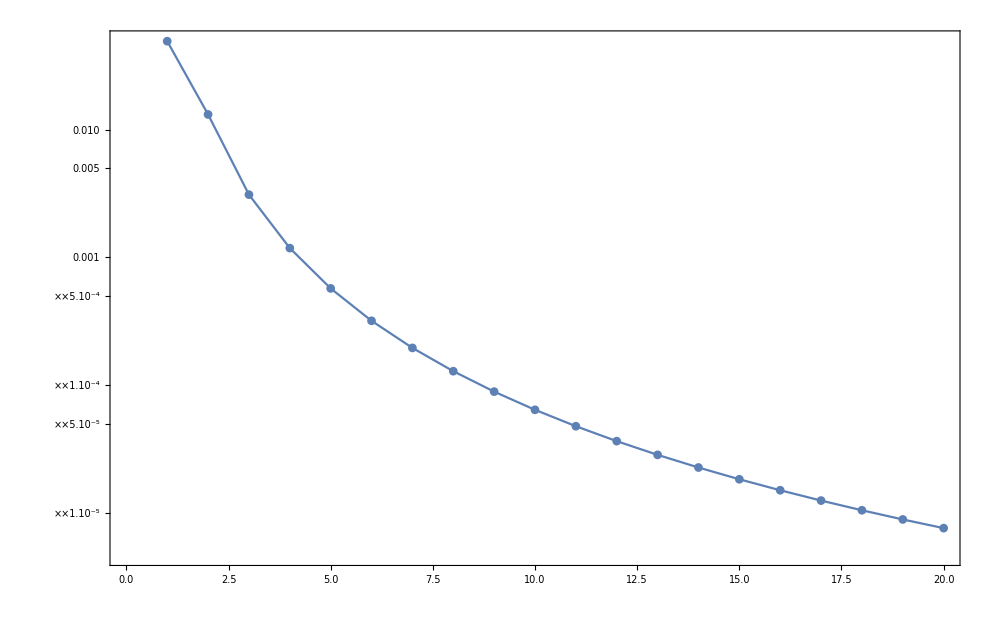

```mathematica
ListLogPlot[Abs@((enV3-energyVs1)/enV3),Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
δVs1=δ50[Vs1[r,a,c1]]
Abs@(δ50V-δVs1)
```

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.918356) is less than WorkingPrecision (50.).

End with 1.1093848s

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.23088) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.032463109876367837828195391284073762058640329354) is less than WorkingPrecision (50.).

{0.001,-0.74286436921857641599581376043787069042836553332695}    1.109385

End with 1.1249983s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010267191500477863555489504126911599334509318983) is less than WorkingPrecision (50.).

End with 1.1406237s

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.01,-0.88852497289787456619239602764434015441476284204743}    1.140624

End with 1.2187474s

{1/1000000,-0.03245171329434496674099204089402953883364199690399}    1.156249

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/1000000000,-0.0010267187892752597979485748151560094751524919624736}    1.234373

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000000+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==228.922) is less than WorkingPrecision (50.).

End with 1.0781213s

{0.003,1.5664280613017292121808802687252424026126823296}    1.078121

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10252382010501138535354572525178932844351601641) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

End with 1.1562594s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.210234) is less than WorkingPrecision (50.).

{1/100000,-0.10216685482114510643116355533906841616750207522762}    1.171884

End with 1.2812606s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.003246766894778080927575398255651009909971305396) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{0.03,-0.20721655807487441436248971089270216191928339726912}    1.281261

End with 1.2656363s

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1/100000000,-0.003246755486257618247232933626171381041817242451376}    1.265636

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0146397) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.9375099s

{0.007,0.014638617088881316083403947848852637619056217679342}    0.9375099

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.3192883805344158892762843660375619437381419526) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 0.9843848s

{1/10000,-0.30905729287939921051536724267830999558868838241477}    0.9843848

NDSolve::precw: The precision of the differential equation ({{2 (1+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010267047580805564070676184964749324655561147818) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.2187746s

{1/10000000,-0.010266686846037179222909082871703398490153823817043}    1.218775

NDSolve::precw: The precision of the differential equation ({{2 (7+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.799324) is less than WorkingPrecision (50.).

End with 1.3437753s

{0.07,0.67432849466689983477483882332862720010277677246894}    1.359391

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.57968) is less than WorkingPrecision (50.).

End with 1.7968936s

{0.3,0.52534438396637716172149299823836686721788104409493}    1.812517

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.156754) is less than WorkingPrecision (50.).

End with 1.4687629s

{0.1,-0.15548842040535908225877408121059056734049047658849}    1.468763

FindRoot::precw: The precision of the argument function (Tan[δ]==6.1157791518469989304133230931785990235408350359) is less than WorkingPrecision (50.).

End with 2.7344026s

{1,1.4087191386033832316075473503131581110132018820522}    2.750027

NDSolve::precw: The precision of the differential equation ({{2 (3+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.06063) is less than WorkingPrecision (50.).

End with 3.6719105s

{0.7,-1.1189867384059290852012622283536289947740266425097}    3.687535

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.1941256417903285014333554072606914930738181043) is less than WorkingPrecision (50.).

End with 6.5625609s

{3,-0.19174081061828787454251062280790756160610274891888}    6.609437

FindRoot::precw: The precision of the argument function (Tan[δ]==-2.0179875347317389337919418861792471132090407737) is less than WorkingPrecision (50.).

End with 10.4532373s

{7,-1.110720510344760827033910895053458820421134873929}    10.484474

NDSolve::precw: The precision of the differential equation ({{2 (10+2.74848340879664406058206781237 Power[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-6.495239472367514790092924267285396586275046904) is less than WorkingPrecision (50.).

End with 11.2501058s

{10,-1.418036849590494934585869749512606934723368902212}    11.296982

{-0.0010267187892752597979485748151560094751524919624736,-0.003246755486257618247232933626171381041817242451376,-0.010266686846037179222909082871703398490153823817043,-0.03245171329434496674099204089402953883364199690399,-0.10216685482114510643116355533906841616750207522762,-0.30905729287939921051536724267830999558868838241477,-0.74286436921857641599581376043787069042836553332695,1.5664280613017292121808802687252424026126823296,0.014638617088881316083403947848852637619056217679342,-0.88852497289787456619239602764434015441476284204743,-0.20721655807487441436248971089270216191928339726912,0.67432849466689983477483882332862720010277677246894,-0.15548842040535908225877408121059056734049047658849,0.52534438396637716172149299823836686721788104409493,-1.1189867384059290852012622283536289947740266425097,1.4087191386033832316075473503131581110132018820522,-0.19174081061828787454251062280790756160610274891888,-1.110720510344760827033910895053458820421134873929,-1.418036849590494934585869749512606934723368902212}

{1.103331243230158196137506847555105154712×10^-12,3.837954845745044086302689242960938298619×10^-11,1.22473673729380225574929437973390357599446×10^-9,3.877568173184429726433826319474771830084135×10^-8,1.2297748813223596261385978005504622510384245×10^-6,0.000039729014183270166518560306362997459464991548,0.0008324562758843241452341119407878314377712812666,0.00094562203340018643264905407318252023744429219,0.00088631728558550746785053989572685575197207250949,0.001081778254783924620678968975213400741375888071,0.00497492444499802165756960124865813615678940630259,0.012020132705505701027750163652266584153891582504,0.0166489523029468019527684246242359277409933229099,0.0539256019043887770509476810375873622630801550294,0.110966754363974308138181988506087726729812063713,0.14133388616295129593561291760065955739119320555,0.24991780932431713330083214387045960212540237977439,0.3040421916688189281931863899360979117257034882039,0.314175916252792898431161750900088016733365848897}

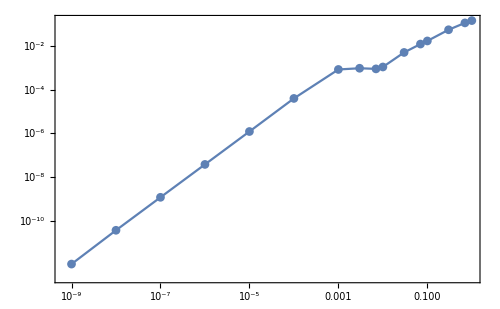

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@(δ50V-δVs1)}],Joined->True,PlotMarkers->Automatic,Frame->True,ImageSize->500]
```

```mathematica
DumpSave["/home/huangys/Desktop/Test_MultipleShortRangePotential_3_enV3.mx",enV3]
```

```mathematica
DumpSave["/home/huangys/Desktop/Test_MultipleShortRangePotential_3_energyVs1.mx",energyVs1]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\Test_MultipleShortRangePotential_3_energyVs1.mx"]
Get["C:\\Users\\ASUS\\Documents\\Test_MultipleShortRangePotential_3_enV3.mx"]
```

DumpGet::bgabi: File C:\Users\ASUS\Documents\Test_MultipleShortRangePotential_3_energyVs1.mx was written with ABI 32, which is not compatible with this version of the Wolfram Language.

$Failed

DumpGet::bgabi: File C:\Users\ASUS\Documents\Test_MultipleShortRangePotential_3_enV3.mx was written with ABI 32, which is not compatible with this version of the Wolfram Language.

$Failed

## Determine 𝒸_2 and 𝒹_1 in V_eff^(a^4)

```mathematica
δexpminus9=δ50e[ee[[2]],V3[r,Fe,Fh]]
```

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010267191489444539492397216607255016731915126363) is less than WorkingPrecision (50.).

End with 0.3125269s

-0.0010267187881719285547184166190185026275973868077613

```mathematica
hhh[en_,c2_?NumberQ,d1_?NumberQ]:=δ50e[en,Vs2[r,a,{c2,d1}]]
evnhhh1:=N[hhh[ee[[1]],c2,d1]-δexpminus10,8];
evnhhh2:=N[hhh[ee[[2]],c2,d1]-δexpminus9,8];
```

```mathematica
Determinec2d1:=Module[{findroot},
findroot=FindRoot[{hhh[ee[[1]],c2,d1]==δexpminus10,hhh[ee[[2]],c2,d1]==δexpminus9},{{c2,-40},{d1,3}},MaxIterations->200,WorkingPrecision->30,StepMonitor:>Print[{c2,d1,evnhhh1,evnhhh2}]];
{c2,d1}/.findroot
]
```

```mathematica
{c2,d1}=Determinec2d1
```

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

End with 1.1558034s

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00078871263141617024602877422370586475283010401903) is less than WorkingPrecision (50.).

End with 1.1147955s

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000000+2.53974543736963879143053219739 Power[«2»]-3. Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.00024941294426371440287759844236422165553196081091) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.2328813s

End with 1.0287378s

End with 0.9977030s

End with 1.0327102s

End with 1.0757584s

End with 1.0897794s

End with 1.1287821s

End with 1.3099234s

End with 0.9176577s

End with 0.9797038s

End with 0.8806080s

End with 0.9696956s

{-35.8667296196216566108699381317,6.16273836845869204031517303652,0.000049352853,0.00015606746}

End with 0.9496827s

End with 0.9897085s

End with 0.9346604s

End with 0.9977038s

End with 0.9436653s

End with 0.9526834s

End with 0.9196640s

End with 1.0237066s

End with 0.9466668s

End with 1.0497418s

{-35.8720792876123248620434697418,5.77688233468726681150231164906,4.8920683×10^-6,0.000015470083}

End with 0.9596762s

End with 1.0117002s

End with 0.9836931s

End with 1.0367320s

End with 0.9216621s

End with 1.0587467s

End with 1.0087204s

End with 0.9756747s

End with 1.0097234s

End with 1.0427366s

{-35.8332069068624880506980243,5.76280042386726262944141606979,6.0773028×10^-8,1.9218126×10^-7}

End with 0.9406753s

End with 0.9336591s

End with 1.0377312s

End with 0.9686696s

End with 0.9736840s

End with 0.9867135s

End with 0.9747001s

End with 0.9466799s

End with 0.9226380s

End with 0.9146570s

{-35.9121689558128499256262257265,5.69624524643331252003248441928,-6.1912455×10^-9,-1.9578443×10^-8}

End with 0.9596766s

End with 0.8856227s

End with 1.0047089s

End with 0.9316453s

End with 0.9756875s

End with 0.9446667s

End with 1.1347990s

End with 1.1137975s

End with 1.1117703s

End with 1.0387326s

{-35.9121707958549807158340012934,5.696304036338259320840967948,9.5564375×10^-14,3.0223934×10^-13}

End with 1.0797625s

End with 1.0687529s

End with 0.9967157s

End with 1.0237217s

End with 0.9886858s

End with 0.9987154s

End with 0.9636790s

End with 1.0157177s

End with 0.9706891s

End with 1.0207194s

{-35.9121707773197480313638252131,5.6963040508626390909463648584,-1.2070272×10^-17,-1.1354756×10^-21}

End with 0.9416528s

End with 1.0307392s

End with 1.0147271s

End with 1.0007045s

End with 0.9906994s

End with 1.0507534s

End with 0.9556738s

End with 1.0397330s

End with 1.0367312s

End with 1.0537343s

{-35.9121707708203832240215123554,5.6963040562821322103092775604,-1.2068758×10^-17,4.9720674×10^-21}

End with 0.9526834s

End with 0.9646795s

End with 0.9736836s

End with 1.0377279s

End with 1.0247107s

End with 1.0637380s

End with 0.9446782s

End with 1.0257219s

End with 0.9947130s

End with 1.0407466s

End with 0.9406506s

End with 1.0517407s

{-35.9121707752076649694884784289,5.69630405262381420810967772439,-1.0491303×10^-17,4.9924548×10^-18}

End with 1.0367319s

End with 1.0237222s

End with 0.9846928s

End with 1.0127142s

End with 0.9386748s

End with 1.0247222s

End with 1.1628302s

End with 1.0617342s

End with 1.0167302s

End with 1.1017648s

End with 1.0187159s

End with 1.0467513s

{-35.9121707773797281605555015725,5.69630405081263266811125284609,-1.1250538×10^-17,2.5911942×10^-18}

End with 1.0407442s

End with 1.0747460s

End with 0.9846920s

End with 1.0207211s

End with 1.0027198s

End with 1.0727544s

End with 0.8896149s

End with 0.9867069s

End with 0.9946995s

End with 1.0167265s

End with 0.9536851s

End with 0.9646688s

End with 1.0107124s

End with 1.0277246s

End with 0.9857061s

End with 1.0457356s

End with 0.9706837s

End with 1.0367307s

End with 0.9716732s

End with 1.0437366s

End with 1.1187848s

End with 0.9917000s

End with 1.0237332s

End with 1.0267372s

End with 1.0207194s

End with 1.0127261s

End with 0.9997073s

End with 0.9997044s

End with 1.0557579s

End with 1.0457368s

End with 1.0337275s

End with 1.1267790s

End with 0.9886985s

End with 1.0517406s

End with 0.9666932s

End with 1.1077942s

{-35.9121707773793699728052809249,5.69630405081293134190986127985,-1.1250604×10^-17,2.5908923×10^-18}

End with 0.9756879s

End with 1.0417348s

End with 1.1338006s

End with 1.0657641s

End with 0.9476563s

End with 1.0267236s

End with 1.0187308s

End with 1.1087938s

End with 0.9926997s

End with 1.0827616s

End with 0.9406511s

End with 1.0297260s

End with 1.0667424s

End with 1.0287374s

End with 1.0157157s

End with 1.0127252s

End with 0.9947007s

End with 0.9947007s

End with 1.0167297s

End with 1.0006939s

End with 0.9996913s

End with 1.0287247s

End with 0.8956450s

End with 0.9656783s

End with 0.9166460s

End with 1.0097115s

End with 1.0026981s

End with 1.0697653s

End with 0.9536740s

End with 0.9646816s

End with 0.9416766s

End with 1.0337181s

End with 0.9516702s

End with 1.0487384s

End with 0.9396744s

End with 1.0357426s

End with 0.9556733s

End with 1.0597492s

End with 0.9506696s

End with 1.0227328s

End with 0.9156451s

End with 1.0127150s

End with 0.9336579s

End with 1.0287386s

End with 0.8876369s

End with 1.0217331s

End with 0.9056496s

End with 1.0477505s

{-35.9121707773793730696891961345,5.69630405081292875955974324258,-1.1250594×10^-17,2.5908876×10^-18}

{-35.9121707773793730696891961345,5.69630405081292875955974324258}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_c2d1.mx",{c2,d1}];
```

```mathematica
energyVs2=EigenEnergy[Vs2[r,a,{c2,d1}],αSch,{1.*10^-15,3000},{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->100}]
```

{-1.60534,-0.180294,-0.0701673,-0.0371042,-0.022911,-0.0155421,-0.0112316,-0.00849419,-0.00664806,-0.0053444,-0.00438975,-0.00366979,-0.00311346,-0.00267467,-0.00232251,-0.00203558,-0.00179872,-0.00160092,-0.00143403,-0.00129194}

ParametricNDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) u[r$50747]-u''[r$50747]/2==e$50746 u[r$50747],u'[3000]==-1.×10^-15,u[3000]==1.×10^-15},{},{},{},{}}) is less than WorkingPrecision (30.).

FindRoot::brdig: The root has been bracketed as closely as possible with 30. working digits but the function value exceeds the absolute tolerance 1.×10^-15.

General::stop: Further output of FindRoot::brdig will be suppressed during this calculation.

{-1.60533833105626567946829457453,-0.180294302917564843312023769098,-0.070167323189144880028495123321,-0.0371042311428744134684269084523,-0.0229109722579912371653717792053,-0.0155420595955763695980602393709,-0.0112315588981504272854789142052,-0.00849419275961009870789611381106,-0.00664806457333931342595844686442,-0.00534440273208723181447841088264,-0.00438975086497215315065061316483,-0.00366979328084502740293445358956,-0.00311345742856570459215005537204,-0.00267467161728450522295878314908,-0.00232250851455901965183808479712,-0.00203558147804919048196289578416,-0.00179871882978815972299094204915,-0.00160091608742053949851307995284,-0.00143403423802306151914357505873,-0.00129194884913595127936147731994}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_energyVs2.mx",energyVs2];
```

```mathematica
EigenEnergySolo[Vs2[r,a ,{c2,d1}],αSch,{1.*10^-15,2000},{0.99 SetPrecision[#,3],1.01 SetPrecision[#,3]}&[-0.02306137918729334],{WorkingPrecision->30,PrecisionGoal->15,MaxStepFraction->10^-1,Method->{"TimeIntegration"->"Adams","EquationSimplification"->{Automatic,
"SimplifySystem"->False},"IndexReduction"->False}},{WorkingPrecision->30,PrecisionGoal->15,MaxIterations->1000}]
```

```mathematica
energyVs2[[5]]=First@%80
```

```mathematica
energyVs2
```

```mathematica
Abs@((energyVs2-enV3)/enV3)
```

{0.07458004634154331834246281377,0.00215075200224280835213258544,0.0001879297221715431640959848,0.00003729878703738777427470243,0.0000110638698411512970385791,4.17384236237793968707814×10^-6,1.8488619682060198025531×10^-6,9.1883127269397532659322×10^-7,4.9791727341364178572372×10^-7,2.8867137917719919118802×10^-7,1.76675596484497265578×10^-7,1.13044315384390286942×10^-7,7.506596357725401436784×10^-8,5.144114735173964235247×10^-8,3.621793830343600577209×10^-8,2.610582378172727125105×10^-8,1.92085442924793810086×10^-8,1.43932200370858531718×10^-8,1.0961314484044311554×10^-8,8.46991074431585298421×10^-9}

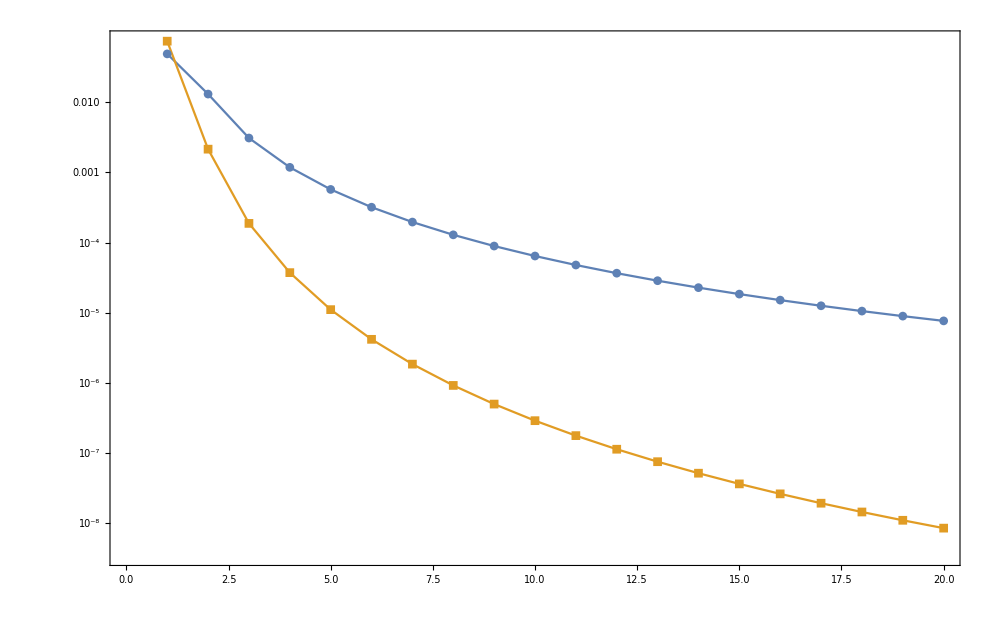

```mathematica
ListLogPlot[{Abs@((energyVs1-enV3)/enV3),Abs@((energyVs2-enV3)/enV3)},Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

```mathematica
δVs2=δ50[Vs2[r,a,{c2,d1}]]
Abs@(δ50V-δVs2)
```

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000000+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/1000000+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.001+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (0.01+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.032463071058512749244805342809652397560038516118) is less than WorkingPrecision (50.).

End with 1.4843835s

{1/1000000,-0.032451674517355095898041790499084718644340676225913}    1.484384

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.916824) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 1.5781342s

{0.001,-0.74203257441587794120065468744527756959701336206678}    1.59376

NDSolve::precw: The precision of the differential equation ({{2 (0.003+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.22819) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0010267191489444513583494018193335570897202478882) is less than WorkingPrecision (50.).

End with 1.7968866s

End with 1.8593874s

{0.01,-0.88745207281202492781991431695400916138084094211354}    1.796887

{1/1000000000,-0.0010267187881719259638308279675060932078940133549161}    1.859387

NDSolve::precw: The precision of the differential equation ({{2 (0.03+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1/100000000+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.0032467668563969129741932947210174188110180012422) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==291.973) is less than WorkingPrecision (50.).

End with 1.5156392s

End with 1.7656420s

{1/100000000,-0.003246755447876854884481457369771765793932532008047}    1.515639

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.10252257737128132876476913562555979100979254367) is less than WorkingPrecision (50.).

{0.003,1.567371368413150790270809944942531554846892299}    1.781267

NDSolve::precw: The precision of the differential equation ({{2 (1/10000000+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

End with 2.0468971s

NDSolve::precw: The precision of the differential equation ({{2 (0.007+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{1/100000,-0.10216562501392644789021907379163923316155504624457}    2.046897

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{2 (1/10000+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.205171) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

End with 2.1093951s

{0.03,-0.20236277458877645092876276620061512243548709721862}    2.109395

NDSolve::precw: The precision of the differential equation ({{2 (0.07+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.010267046355897808050560694162284931555964283355) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

FindRoot::precw: The precision of the argument function (Tan[δ]==0.0155211) is less than WorkingPrecision (50.).

End with 1.4531387s

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.31924460401608176015866284371705867379199609131) is less than WorkingPrecision (50.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

{1/10000000,-0.01026668562125852988019867055889141368013472337602}    1.468763

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

End with 1.5156395s

End with 1.4062629s

{0.007,0.015519843810581207174254960059767334027881012801793}    1.51564

NDSolve::precw: The precision of the differential equation ({{2 (0.3+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

{1/10000,-0.30901756578702051578269798861603229727831453706627}    1.421888

NDSolve::precw: The precision of the differential equation ({{2 (7+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{2 (1+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==0.8181) is less than WorkingPrecision (50.).

End with 1.8281419s

{0.07,0.6856807371492548760522951775598413428401586092225}    1.843768

NDSolve::precw: The precision of the differential equation ({{2 (0.1+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.14106) is less than WorkingPrecision (50.).

End with 1.8125173s

{0.1,-0.14013535931835281743339993743710064957524488374157}    1.828143

FindRoot::precw: The precision of the argument function (Tan[δ]==0.638364) is less than WorkingPrecision (50.).

End with 2.8437767s

{0.3,0.56815184898465271727762768762812302049646596607218}    2.859401

NDSolve::precw: The precision of the differential equation ({{2 (0.7+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==11.42792354151546388302508601829644499494321102) is less than WorkingPrecision (50.).

End with 5.1250480s

{1,1.483513690872589918573073311415849874673244938105}    5.156299

NDSolve::precw: The precision of the differential equation ({{2 (3+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.74562) is less than WorkingPrecision (50.).

End with 4.5000429s

{0.7,-1.0505688002166944486024261240602775317001125849195}    4.515668

FindRoot::precw: The precision of the argument function (Tan[δ]==-1.7260232635613923656764860067981797290030573264) is less than WorkingPrecision (50.).

End with 13.7188794s

{7,-1.0456867230751614508742795946093448212937600703699}    13.765756

NDSolve::precw: The precision of the differential equation ({{2 (10+2.28019429694721342438653015745 Power[«2»]-5.69630405081292875955974324258 Plus[«2»]+Power[«2»] Erf[«1»]) u[r]+u''[r]==0,u'[1/100000000000000000000]==1,u[1/100000000000000000000]==1/100000000000000000000},{},{},{},{}}) is less than WorkingPrecision (50.).

FindRoot::precw: The precision of the argument function (Tan[δ]==-0.1154865801369528512858669973891718542944559201) is less than WorkingPrecision (50.).

End with 9.1407111s

{3,-0.11497722931771721162293278741639081546571149544466}    9.1563361

FindRoot::precw: The precision of the argument function (Tan[δ]==-4.662556322539997102184794525243948034832634971) is less than WorkingPrecision (50.).

End with 14.9220147s

{10,-1.359522387349738964451429760113441933710040056005}    14.96889

{-0.0010267187881719259638308279675060932078940133549161,-0.003246755447876854884481457369771765793932532008047,-0.01026668562125852988019867055889141368013472337602,-0.032451674517355095898041790499084718644340676225913,-0.10216562501392644789021907379163923316155504624457,-0.30901756578702051578269798861603229727831453706627,-0.74203257441587794120065468744527756959701336206678,1.567371368413150790270809944942531554846892299,0.015519843810581207174254960059767334027881012801793,-0.88745207281202492781991431695400916138084094211354,-0.20236277458877645092876276620061512243548709721862,0.6856807371492548760522951775598413428401586092225,-0.14013535931835281743339993743710064957524488374157,0.56815184898465271727762768762812302049646596607218,-1.0505688002166944486024261240602775317001125849195,1.483513690872589918573073311415849874673244938105,-0.11497722931771721162293278741639081546571149544466,-1.0456867230751614508742795946093448212937600703699,-1.359522387349738964451429760113441933710040056005}

{2.5908875886515124094197033734528452×10^-18,1.214905301035393372722818275327457139×10^-15,4.1912048908156563517605076115524446563×10^-14,1.30813899865298605668162544158301983673×10^-12,3.233733618131834294962863254369599055856×10^-11,1.9218045754338493062440852991490911461995×10^-9,6.614731858493500750389481947106064191100064×10^-7,2.3149219786083427193778558933680032343228×10^-6,5.090563885616376999527684812159343147277387038×10^-6,8.8781689342862481972582848824077074539881371×10^-6,0.0001211409589000582238426565565710966729931062521,0.0006678902231506597502938094210524414165097457502,0.001295891215940537127394280850746009975747730063,0.011118136886113221494812991647831208984495233052,0.042548816174739671539345884212736263655898006123,0.066539333893744608970086956497967793731150149493,0.17315422802374647038125430847894285598501112630017,0.2390084043992195520335550894919839125983286846448,0.25566145401203692829672176150092301572003700269}

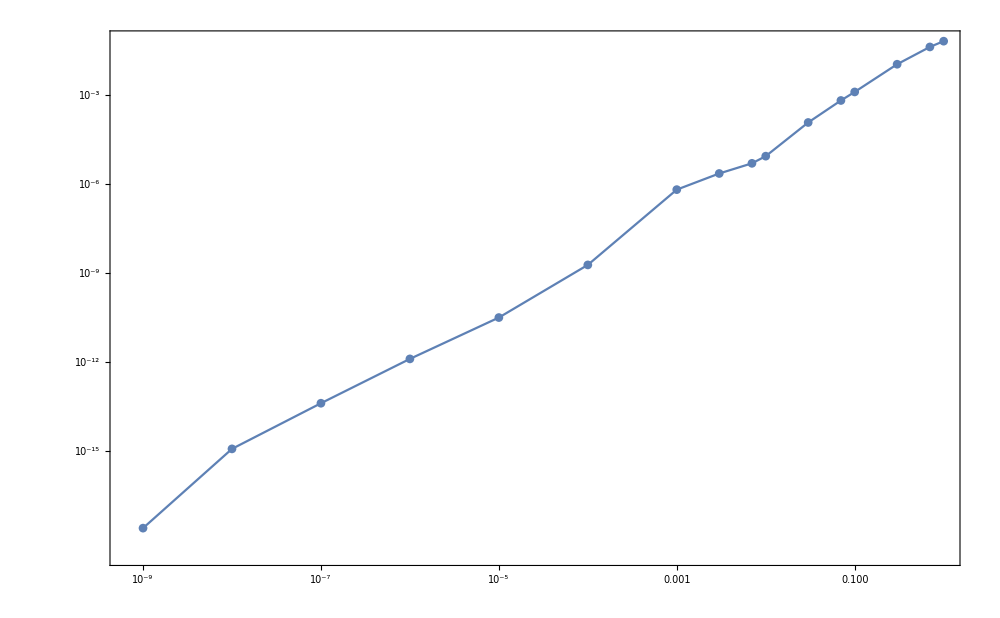

```mathematica
ListLogLogPlot[Transpose[{Drop[ee,1]}~Join~{Abs@(δ50V-δVs2)}],Joined->True,Frame->True,ImageSize->1000,PlotMarkers->Automatic]
```

## Matrix element <p^4>

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_energyVs1.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_c1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_energyVs2.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_c2d1.mx"]
```

```mathematica
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_efV3.mx"]
Get["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_efVs2.mx"]
```

```mathematica
nRange=20;
```

```mathematica
AbsoluteTiming[efV3=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[V3[r,Fe,Fh],enV3[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4,StartingStepSize->0.0001];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-1.49392158966818070097458056441 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0371056151373113113151434204534 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0112315796637909105446479489882 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00534440427486378471992629803055 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.022911225744810778986512265203 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00849420056434721376492999788875 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00438975164053414266082069251954 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.180682907041655735601681177112 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0155421244659538669469224973398 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00664806788352714746059600286795 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00366979369569434333465299693612 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0701805121933032241007816029845 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00311345766228040406821329689727 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00232250859867549278786669726095 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00179871886433893069836350333203 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00143403425374196195530101812417 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00267467175487268908290083501705 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.0020355815311897232285403855934 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00160091611046287733732091511492 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-Power[«2»]-1.0340694151301588199487468955339863896369934082031 Power[«2»] Power[«2»]) f[r]-f''[r]/2==-0.00129194886007864281044819264799 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1798.67,{2.78659257818×10^-1453                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-8.43103740918×10^-469                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.97118×10^-269                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.6756×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],5.77714×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.60722×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.54193×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.76482×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.96256×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.22317×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.8271×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000159251                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],91.6723                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.97114×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.24338×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.92149×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0187866                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2876.95                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.29878×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.44822×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

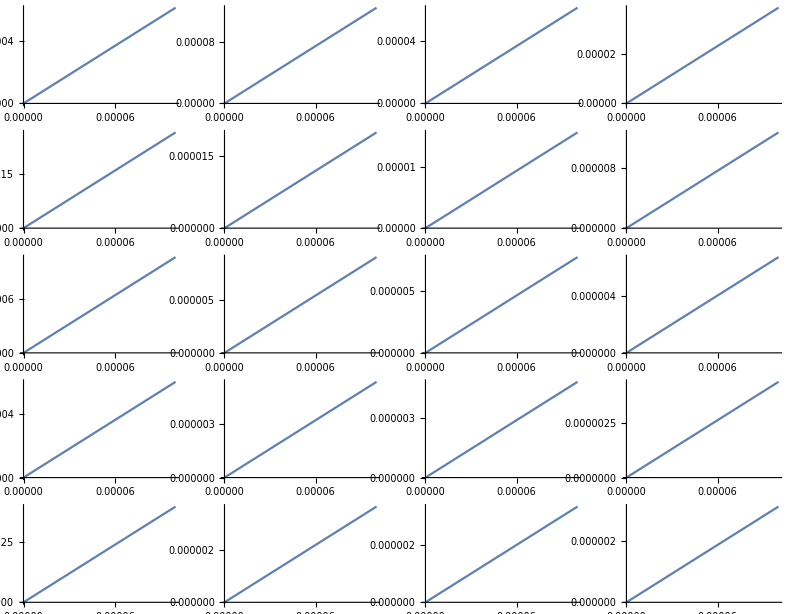

```mathematica
GraphicsGrid@Partition[Table[Plot[efV3[[n]],{r,0,0.0001},ImageSize->Small,AxesOrigin->{0,0},PlotRange->Full],{n,1,20}],4]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_efV3.mx",efV3];
```

```mathematica
AbsoluteTiming[efVs2=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs2[r,a,{c2,d1}],energyVs2[[n]],r,{Which[n<14,2000,n<20,3000,n==20,4000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-1.60533833105626567946829457453 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0371042311428744134684269084523 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0112315588981504272854789142052 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00534440273208723181447841088264 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00438975086497215315065061316483 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0229109722579912371653717792053 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00849419275961009870789611381106 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.180294302917564843312023769098 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00366979328084502740293445358956 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.0155420595955763695980602393709 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00664806457333931342595844686442 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.070167323189144880028495123321 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00311345742856570459215005537204 f[r],f[2000]==1.×10^-50,f'[2000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00232250851455901965183808479712 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00179871882978815972299094204915 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00143403423802306151914357505873 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00267467161728450522295878314908 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00203558147804919048196289578416 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00160091608742053949851307995284 f[r],f[3000]==1.×10^-50,f'[3000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::precw: The precision of the differential equation ({{(-2.28019429694721342438653015745 Power[«2»]+5.69630405081292875955974324258 Plus[«2»]-Power[«2»] Erf[«1»]) f[r]-f''[r]/2==-0.00129194884913595127936147731994 f[r],f[4000]==1.×10^-50,f'[4000]==-1.×10^-50},{},{},{},{}}) is less than WorkingPrecision (50.).

{1837.57,{3.23937375893×10^-1508                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-3.11494784066×10^-468                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],2.11771×10^-269                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.69321×10^-178                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],5.7914×10^-126                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-1.60847×10^-91                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],4.54328×10^-67                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-9.76609×10^-49                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.96268×10^-34                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-6.22338×10^-23                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],1.82714×10^-13                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-0.0000159252                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],91.6729                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 2000.0000000000000000000000000000000000000000000000}}, <>][r],-2.97116×10^-22                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],8.24341×10^-15                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2.92149×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],0.0187866                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-2876.95                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],1.29878×10^8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 3000.0000000000000000000000000000000000000000000000}}, <>][r],-6.44822×10^-8                                                                              -51
InterpolatingFunction[{{9.999999999999998889216268837848585141837807946682 10   , 4000.0000000000000000000000000000000000000000000000}}, <>][r]}}

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_MultipleShortRangePotential_3_efVs2.mx",efVs2];
```

```mathematica
p4Ture[n_,b_][Z_,γ_,η_,opt___]:=Z NIntegrate[(Laplacian[efVs2[[n]],{r}]^2),{r,0,If[n>15,4000,b]},opt]+γ/a NIntegrate[efVs2[[n]]^2 δa[r],{r,0,If[n>15,4000,b]},opt]+η a NIntegrate[efVs2[[n]]^2 Laplacian[δa[r],{r,θ,ϕ},"Spherical"],{r,0,b},opt]
```

```mathematica
Plot[Evaluate@D[efV3[[1]],{r,2}],{r,0,10^-40},PlotRange->All]
```

```mathematica
NIntegrate[D[efV3[[1]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]
```

NIntegrate::precw: The precision of the argument function (7.76509819679×10^-2906 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},«38»,{46,45},{47,46},{48,47},{49,48},{50,49},«58543»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.978731816765628615596634062628021767125602381327474109199831794029252202484543473749171640054592744×10^-20}. NIntegrate obtained 98.45362228616327540609455612150923573414733534075230383947322507870653341416465683385981746778945007 and 4.122817400324200516524366135679977709664487291051248137882893637494278659636989639731676625155904079×10^-18 for the integral and error estimates.

98.453622286163275406094556121509235734147335340752

```mathematica
REAL=Table[NIntegrate[D[efV3[[n]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,nRange}];
N[%,6]
REF=Table[NIntegrate[D[efV3[[n]],{r,2}]^2,{r,10^-20,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}],{n,nRange-2,nRange}];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (7.76509819679×10^-2906 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},«38»,{46,45},{47,46},{48,47},{49,48},{50,49},«58543»},«1»}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {1.978731816765628615596634062628021767125602381327474109199831794029252202484543473749171640054592744×10^-20}. NIntegrate obtained 98.45362228616327540609455612150923573414733534075230383947322507870653341416465683385981746778945007 and 4.122817400324200516524366135679977709664487291051248137882893637494278659636989639731676625155904079×10^-18 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (7.1082391795×10^-937 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},«39»,{46,45},{47,46},{48,47},{49,48},{50,49},«20485»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.630673174393802462898376591556691051516589195615436873540378424413931011231507726782094864325827654×10^-20}. NIntegrate obtained 5.048073978359864897228262581022587169726502429892434878764925780264046593812250635089041042685065874 and 1.621461340608101392166656123976004020940290262019977129945922083848940429388146218541184751101388768×10^-19 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (3.88554105316787×10^-538 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},«39»,{46,45},{47,46},{48,47},{49,48},{50,49},«14852»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.274912128709863061114042719895662978913114958567045177837231596470428577827096331679901760095505554 and 5.583018528589881227284289346358435831851233968690093895509694990633179494308470864373808522096941736×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {3.741115325219046535249679347659646860326860262695791817645251222873374564511742429498127653010877883×10^-20}. NIntegrate obtained 0.4985817504820395181707512212667188504271337065021149537064520138113580608224799600988364267672451509 and 1.666924886209572108822267582441740945169117528522335127513697170003283970400654726618888836487500533×10^-20 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.1371682600325772916378897204244740879984506094160058459844057585534996206401804250084670828184037266 and 6.069386431696235383518948462537272288436921866632998891155050375323964169843963046246637511064177578×10^-22 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.02794475433779497233151894890573837433947838025329149207002700934601890045311065450624230448798534805 and 3.897925986818154235619471782066427786719279619501706254862552006005355782983998568816989649382753232×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{98.4536,5.04807,1.27491,0.498582,0.244124,0.137168,0.084588,0.0557863,0.038707,0.0279448,0.0208294,0.0159383,0.0124661,0.00993343,0.00804285,0.00660314,0.00548751,0.00460969,0.00390953,0.00334428}

NIntegrate::precw: The precision of the argument function (8.27685×10^6 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{2,1},{2,1},{3,2},{4,3},{5,4},{6,5},{7,6},{8,7},«35»,{44,43},{45,44},{46,45},{47,46},{48,47},{49,48},{50,49},«11338»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.004609686899976843195818140641408963729848763600482551579594395549586062393203939466940908809880004152 and 8.638179300972808752517157633018970039433755103874745599371062333228277164954512003248628478699177638×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.68683×10^16 («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.003909533854867483163735885812356002870491955540261914938535587925733633856455751743902662035330752568 and 1.470279646198827173803712009072073555641189154968349834344138769926534919086030838651868469310088045×10^-22 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (4.15795×10^-15 («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.003344284438271613803929943962179038053928644797643978071001911629514805935407049978303885635238946377 and 1.469253535462073410830835280454550468764789097553250629835612711900068115139420118016570907269126578×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{0.00460969,0.00390953,0.00334428}

### Matrix element in V_eff^(a^2)

```mathematica
AbsoluteTiming@Module[{n=19},ef=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{4000,1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
ef=If[OddQ[n],ef,-ef];
GraphicsGrid@{{Plot[{ef,r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium],
Plot[{ef-r RS[n,r]},{r,0,2000},PlotRange->Full,ImageSize->Medium]}}
]
```

```mathematica
NIntegrate[(D[ef,{r,2}])^2,{r,1.*10^-50,4000},Exclusions->50]
Abs@((%-REAL[[20]])/REAL[[20]])
```

```mathematica
AbsoluteTiming[efVs1=Module[{efunction=Range@20},
SetSharedVariable[efunction];
ParallelTable[
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]],{n,1,20}];
efunction
]]
```

```mathematica
Module[{n=14,efunction},
efunction[[n]]=First@Eigenfunsin[Vs1[r,a,c1],energyVs1[[n]],r,{If[n>15,4000,2000],1.*10^-50},WorkingPrecision->50,PrecisionGoal->15,InterpolationOrder->All,MaxSteps->Infinity,MaxStepFraction->10^-4];
efunction[[n]]=If[OddQ[n],efunction[[n]],-efunction[[n]]];
efVs1[[n]]=efunction[[n]]
]
```

```mathematica
DumpSave["C:\\Users\\ASUS\\Documents\\DataDump_Coulomb_7_efVs1_3rd.mx",efVs1];
```

```mathematica
FALSEVs1=NIntegrate[D[efVs1[[#]],{r,2}]^2,{r,0,If[#>15,4000,2000]},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs1)/REAL);
N[%,6]
```

```mathematica
RESVs1=FindRoot[Evaluate@Thread[(p4Ture[#,If[#>15,4000,2000]][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{(*15,*)20})==(REF[[#]]&/@{(*2,*)3})](*/.Z->1*),{γ,-1,-10},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10,MaxIterations->10000]
((p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{15,20})-(REF[[#]]&/@{2,3}))/(REF[[#]]&/@{2,3})/.RESVs1
```

```mathematica
p4Vs1=p4Ture[#,2000][1,γ,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs1;
N[%,6]
Abs[(p4Vs1-REAL)/REAL];
N[%,6]
```

```mathematica
ListLogPlot[%161,Joined->True,PlotMarkers->{Automatic}]
```

### Matrix element in V_eff^(a^4)

```mathematica
FALSEVs2=NIntegrate[D[efVs2[[#]],{r,2}]^2,{r,0,2000},{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange;
N[%,6]
Abs@((REAL-FALSEVs2)/REAL);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (1.049354235×10^-3015 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},«33»,{42},{43},{44},{45},{46},{47},{48},{49},«60632»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.098473923994854608021114590514965879878034520385465910236082243767783005129989048873573021882712542}. NIntegrate obtained 7.245859645635543805010206154119412854500172247526108626430897510695034662739133945286208241869227461 and 1.580637122374187458229895229428011697464596830544634268073223427549365741440578441826343118246101768×10^-20 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (9.70290005002×10^-936 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},«33»,{42},{43},{44},{45},{46},{47},{48},{49},«20356»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69785887335938799373453277973018370609627510090422917790776576893839284561559148539521729643703425 and 3.93492107888425152966968333784435561445513097241877019851431717808261385534354054183293200071895161×10^-21 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (4.48468209737865×10^-538 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.4540851973078978474621378235112907984173854579256769632173442686149149327413245705993575939918169214 and 3.989606392726136961307537774675792136288173084074503693504518144805847291874190806286917626109802183×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.5881850405378984744476577474411129732638295171484669868062073194672234500148220814506599588600705935}. NIntegrate obtained 0.1812145983039278501231942641258180983769472499009298281821852395864993306752562482457676518238308436 and 2.598854068894769957823432680748167622252692638462615854657670279490631509746267521423687154184427547×10^-18 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08971920602054963185823516453214893441677439654321364258054790581071129929784362857221801991636574221 and 5.877868940833922302088501059675869278456199960126675449143757459255242862002011027460256628227020087×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.4920968561096776369284592087162242887255853559923368684669518800539484255382534094076722843679116121}. NIntegrate obtained 0.02082694317808067693857321972106020861681545167383972851438641858188716447507450444333246627692357665 and 2.148420104022565063492136488241059088707990702429844264803692346684913909313093430203638297225257539×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{7.24586,1.69786,0.454085,0.181215,0.0897192,0.0507705,0.0314643,0.0208269,0.0144914,0.0104855,0.00782987,0.00600031,0.00469908,0.00374845,0.00303787,0.00249611,0.00207588,0.00174491,0.00148073,0.00126729}

{0.926403,0.663662,0.64383,0.63654,0.632486,0.629867,0.628029,0.626666,0.625614,0.624777,0.624095,0.623529,0.623051,0.622643,0.62229,0.621981,0.621709,0.621468,0.621252,0.621059}

```mathematica
RESVs2=FindRoot[Evaluate@Thread[(p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@{18,19,20})==(REF[[#]]&/@{1,2,3})](*/.Z->1*),{{Z,1.1,1.12},{γ,0,100},{η,100,-2}},WorkingPrecision->50,AccuracyGoal->10,PrecisionGoal->10]
```

NIntegrate::precw: The precision of the argument function (8.27687×10^6 («1»)^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001744914034173142650708809584451543271507202572845911263270380374669630427211794452549368632286525211 and 3.91737050717735336064712548348382621332653477047591016088146524029509376660907309431482415444791565×10^-23 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (525528. ⅇ^(-r^2/2) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,3000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},«27»,{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},«10985»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.571406450043233714330678554215196776537753180481593290767189102239467422060864659377596605673759215}. NIntegrate obtained 2.329971141656566592285463913292128784015094040944568877305523869908158319075097298568554484269494376×10^-6 and 7.777271092424994672988430524336990453056494790752862066385695798571131870264000172668966259989268606×10^-30 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (8.27687×10^6 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) («1»)^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.571406475432914370600952769503293367563375737548519406477223965236301847467509043536705285818448192}. NIntegrate obtained -2.790644932819551989202805059340554548254626051075427255707410006443353627467776554539775557454279218×10^-6 and 2.518023564153160081887649911239593717319493462261701766375013552086910522626384633248758629084065892×10^-29 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.001480726682451921854597689133072611827608840797810018104114289692303945678817241936169656917789031502 and 1.772672121402613485617239706193548939855125789458732652178601781943813026487599751382455008816115314×10^-22 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {0.6652688690132393210351703059634439647097330475617481444367468319696019146536945240013525850281983215}. NIntegrate obtained 1.975213615936746514400068699823066095718038805849770870639707440659238498071222936903350941956143695×10^-6 and 2.401626230333446479159024375759487157094137704626733711641274903132676614230922757843618779085416839×10^-28 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{Z→0.99979195422191656453551485758782989723540759381604,γ→399.03159555584984095369775930627639745551687370131,η→-693.53279694807759996880070787239541265676875818833}

```mathematica
p4Vs2=p4Ture[#,2000][Z,γ,η,{MaxRecursion->30,WorkingPrecision->50,AccuracyGoal->30}]&/@Range@nRange/.RESVs2;
N[%,6]
Abs[(p4Vs2-REAL)/REAL];
N[%,6]
```

NIntegrate::precw: The precision of the argument function (1.049354235×10^-3015 (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},«33»,{42},{43},{44},{45},{46},{47},{48},{49},«60632»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.098473923994854608021114590514965879878034520385465910236082243767783005129989048873573021882712542}. NIntegrate obtained 7.245859645635543805010206154119412854500172247526108626430897510695034662739133945286208241869227461 and 1.580637122374187458229895229428011697464596830544634268073223427549365741440578441826343118246101768×10^-20 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (6.66273157633×10^-3017 ⅇ^(-r^2/2) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},«33»,{42},{43},{44},{45},{46},{47},{48},{49},«60632»},{«1»}}}][r])^2) is less than WorkingPrecision (50.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.098470689979361104569081957937347504740920962841968908928542979993409925013268923376145212802133534}. NIntegrate obtained 0.03919381150708522645052037857404433504042181733324976937651477546775240755129641859916881097243522907 and 5.221562765822467888382275644996328689436037316850143178615731349751414347537464002951027434039114662×10^-24 for the integral and error estimates.

NIntegrate::precw: The precision of the argument function (1.049354235×10^-3015 (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) (InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«3»,{{{{1},{1},{2},{3},{4},{5},{6},{7},{8},«33»,{42},{43},{44},{45},{46},{47},{48},{49},«60632»},{«1»}}}]«1»«1»])^2) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 30 recursive bisections in r near {r} = {2.098470689979361104569081957937347504740920962841968908928542979993409925013268923376145212802133534}. NIntegrate obtained -0.08635571824164536866175966809574262170933281304593770968115620577371923902110043843191611689900831687 and 7.450711649136597700638579452984394424585337799912377033521706907764503779869632888687860065044530971×10^-24 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.69785887335938799373453277973018370609627510090422917790776576893839284561559148539521729643703425 and 3.93492107888425152966968333784435561445513097241877019851431717808261385534354054183293200071895161×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.4540851973078978474621378235112907984173854579256769632173442686149149327413245705993575939918169214 and 3.989606392726136961307537774675792136288173084074503693504518144805847291874190806286917626109802183×10^-21 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.08971920602054963185823516453214893441677439654321364258054790581071129929784362857221801991636574221 and 5.877868940833922302088501059675869278456199960126675449143757459255242862002011027460256628227020087×10^-22 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{82.7744,4.92061,1.27124,0.498233,0.244065,0.137154,0.0845839,0.055785,0.0387065,0.0279445,0.0208293,0.0159383,0.0124661,0.00993342,0.00804285,0.00660314,0.00548751,0.00460969,0.00390953,0.00334428}

{0.159254,0.0252491,0.00288231,0.00069999,0.000241094,0.000101184,0.0000480522,0.0000247435,0.000013438,7.54626×10^-6,4.30839×10^-6,2.4628×10^-6,1.38203×10^-6,7.47319×10^-7,3.75253×10^-7,1.6312×10^-7,5.22955×10^-8,0.,0.,0.}

## ψ_0 in effective theory

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
REALψ0=NLimit[efV3[[#]]/(r √(4π)),r->0]&/@Range@nRange
REF=NLimit[efV3[[#]]/(r √(4π)),r->0]&/@{19,20};
```

{1.72668,0.352353,0.174331,0.108299,0.0755029,0.0564634,0.044268,0.0359073,0.0298825,0.0253723,0.0218925,0.0191412,0.0169214,0.0150998,0.0135831,0.0123042,0.0112142,0.0102761,0.00946188,0.00874977}

```mathematica
FALSEψ0=NLimit[efVs2[[#]]/(√(4π)r),r->0,Scale->10]&/@Range@nRange
N[%,6]
Abs@((REALψ0-FALSEψ0)/REALψ0);
N[%,6]
```

{0.568698,0.187563,0.0928854,0.0576366,0.0401577,0.0300209,0.0235319,0.0190849,0.0158813,0.0134834,0.0116336,0.0101712,0.00899142,0.00802331,0.00721725,0.00653767,0.00595842,0.00545993,0.00502727,0.00464888}

{0.568698,0.187563,0.0928854,0.0576366,0.0401577,0.0300209,0.0235319,0.0190849,0.0158813,0.0134834,0.0116336,0.0101712,0.00899142,0.00802331,0.00721725,0.00653767,0.00595842,0.00545993,0.00502727,0.00464888}

{0.670641,0.467686,0.46719,0.467801,0.468129,0.468313,0.468423,0.468494,0.468543,0.468577,0.468603,0.468622,0.468637,0.468649,0.468658,0.468666,0.468672,0.468677,0.468682,0.468686}

```mathematica
ψ0True[n_,d_][γ_,η_,{optpsi___}]:=√(4π)(γ NIntegrate[efVs2[[n]]/r δa[r] r^2,{r,0,d},optpsi]+η a^2 NIntegrate[efVs2[[n]]/r Laplacian[δa[r],{r,θ,ϕ},"Spherical"] r^2,{r,0,d},optpsi])
```

```mathematica
RES=FindRoot[Thread[ψ0True[#,2000][γ,η,{MaxRecursion->20}]&/@{19,20}==(REF[[#]]&/@{1,2})],{{γ,0,-2},{η,0,-2}},AccuracyGoal->10,MaxIterations->100000,WorkingPrecision->30]
```

FindRoot::precw: The precision of the argument function ({2 √π (-0.0000487653 γ-0.00057909 η)==0.00946188,2 √π (-0.0000451 γ-0.000535439 η)==0.00874977}) is less than WorkingPrecision (30.).

{γ→-29.6901929515380349872052792157,η→-2.10898948101989711860242267025}

```mathematica
ψ0Vs1=ψ0True[#,If[#>15,4000,2000]][γ,η,{MaxRecursion->20}]&/@Range@nRange/.RES;
N[%,6]
Abs@((REALψ0-ψ0Vs1)/REALψ0);
N[%,6]
```

NIntegrate::precw: The precision of the argument function (2.05679618104×10^-1509 ⅇ^(-r^2/2) r «1») is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (3.23937375893×10^-1508 r (-(3 ⅇ^(-r^2/2))/(2 √2 π^(3/2))+(ⅇ^(-r^2/2) r^2)/(2 √2 π^(3/2))) InterpolatingFunction[{{9.9999999999999988892162688378485851418378079466825×10^-51,2000.}},«4»][r]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function («1») is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

{-3.87545,0.342517,0.173715,0.108201,0.0754787,0.0564557,0.0442651,0.035906,0.029882,0.025372,0.0218923,0.0191411,0.0169214,0.0150998,0.0135831,0.0123042,0.0112142,0.0102761,0.00946188,0.00874977}

{3.24445,0.0279163,0.0035345,0.00090311,0.000320125,0.000136873,0.0000659038,0.0000343549,0.0000188998,0.0000107727,6.27263×10^-6,3.68374×10^-6,2.15907×10^-6,1.24163×10^-6,6.88835×10^-7,3.57645×10^-7,1.68491×10^-7,6.26546×10^-8,8.12738×10^-10,8.10196×10^-10}